## Осипов Никита, ПМ-1801 (1.3.6) Паде - аппроксимация [n/n+2]

[n/n+2]
Матрица для нахождения коэффициентов b_i при [n/n+2];
		{{C_-1, C_(0,)C_1, ......., C_n},
l =   {C_(0,)C_(1,)...........,C_(n+1)},
		......................,
		{C_n, C_(n+1),.......,C_(n+n+1)}}

```mathematica
Clear@x;
f1=√((1+x/2)/(1+2 x));
f2=Sin[x];
```

taylor - Функция для нахождения коэффициентов ряда Тейлора;

```mathematica
Clear@x;
taylor[f_,n_]:=Module[{r,test={},z},
z=Table[Clear@x;r=D[f,{x,t}]/(t!);x=0;AppendTo[test,r] ,{t,0,n}];
z⟦-1⟧];
```

apPade - Паде - аппроксимация.

```mathematica
apPade[f_,n_]:=Module[{l={},c,r,b,a,sta=0,stb=0},
Clear@x;
c = taylor[f,2*n+3];
AppendTo[l,Flatten@{0,c⟦#⟧&/@Range[n+1]}];(*{Subscript[C, -1], C_(0,)Subscript[C, 1], ......., Subscript[C, n]}*)
For[i = 1,i≤n+1,i++,
AppendTo[l,c⟦#⟧&/@Range[i,n+1+i]]];(*Заполнение матрицы l*)
r = -(c⟦#⟧&/@Range[n+2,2*n+3]);(*Результат произведение матрицы l на {Subscript[b, 1], ..., Subscript[b, j]}*)
b = N@#&/@(Flatten[{1,Reverse[Inverse[l].r]}]);
a={c⟦1⟧};
For[L=2,L≤n+1,L++,
AppendTo[a,c⟦L⟧+∑_(k=2)^L b⟦k⟧*c⟦L-k+1⟧]];
a = N@#&/@a;
Clear@x;
a=Normal@Plus@@(#*x^(sta++)&/@a);(*Subscript[a, 0]+Subscript[a, 1] x+Subscript[a, 2] x^2+..+Subscript[a, n] x^n*)
b=Normal@Plus@@(#*x^(stb++)&/@b);(*Subscript[b, 0]+Subscript[b, 1] x+Subscript[b, 2] x^2+..+Subscript[b, n+2] x^(n+2)*)
a/b];
```

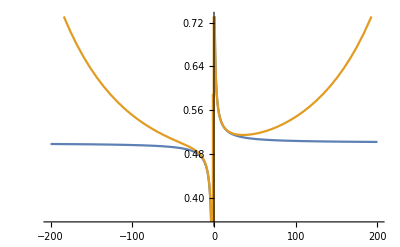
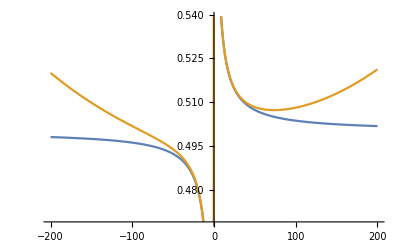
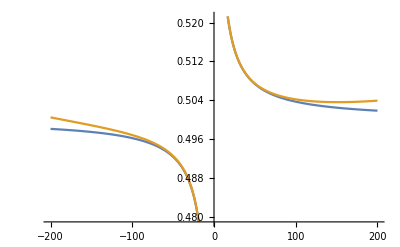
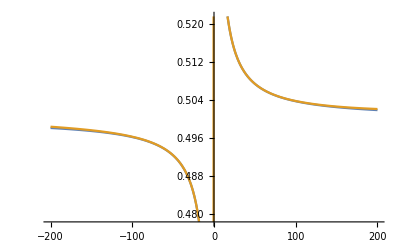
√((1+x/2)/(1+2 x))n = 5 | n = 6 | n = 7 | n = 8
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
appr=Table[apPade[f1,t],{t,5,8}];
Row[{f1,,Grid[{"n = "<>ToString@#&/@Range[5,8],
Flatten@Transpose[{Plot[{f1,appr⟦#⟧},{x,-200,200}]}&/@Range[1,4]]},
Frame->All]}]
```

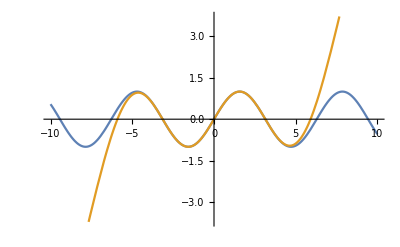
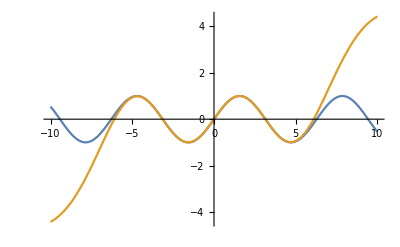
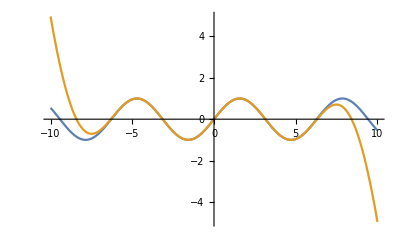
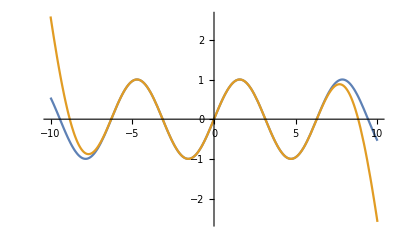
Sin[x]n = 5 | n = 6 | n = 7 | n = 8
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
appr=Table[apPade[f2,t],{t,5,8}];
Row[{f2, ,Grid[{"n = "<>ToString@#&/@Range[5,8],
Flatten@Transpose[{Plot[{f2,appr⟦#⟧},{x,-10,10}]}&/@Range[1,4]]},
Frame->All]}]
```